-Graphics-

```mathematica
dataraw=Import[NotebookDirectory[]<>"FlukaData.xlsx","XLSX"][[1]];
```

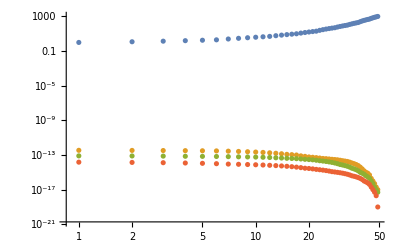

```mathematica
ListLogLogPlot[Transpose[dataraw]]
```

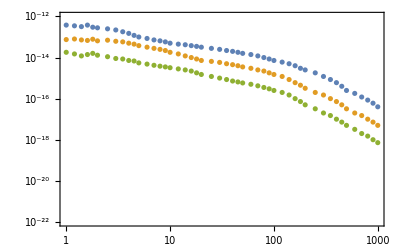

```mathematica
ListLogLogPlot[{{#[[1]],#[[2]]}&/@dataraw,{#[[1]],#[[3]]}&/@dataraw,{#[[1]],#[[4]]}&/@dataraw},Frame->True,GridLines->Full,PlotRange->{{1,10^3},{10^-22,10^-12}}]
```

I tried different LLMs and asked them to extract data, they never properly do so. Here are the comparison of the best extracted data...-Graphics-

Absorption constant per meter, the flux shall be Exp[-L/\lambda] and this is to extract the mean value of \lambda in units of meter*)

This uses the first 12 bins, up to 5 MeV, where the extracted data is close to the Fluka distribution. If one extracts the data manually, one can extend the range of data*)

```mathematica
lengthtable={274,335,396};
data2use4calculation=dataraw[[1;;12]];
Log[(#[[4]]/#[[2]])&/@data2use4calculation]/(lengthtable[[1]]-lengthtable[[3]])*100
(*Mean and deviation by comparing bin-by-bin*)
meanstd1={Mean[%],StandardDeviation[%]}
(*Using the above mean we can do another statistical test from the three data points per energy*)
(Log[(#[[4]]/#[[3]])&/@data2use4calculation]/(lengthtable[[2]]-lengthtable[[3]])*100-meanstd1[[1]]);
(Log[(#[[2]]/#[[3]])&/@data2use4calculation]/(lengthtable[[2]]-lengthtable[[1]])*100-meanstd1[[1]]);
Sqrt[(%^2+%%^2)/2]
std2=Sqrt[Total[(%^2+%%^2)]/(2*Length[data2use4calculation])]
Print[meanstd1[[1]]±%]
(*The flux reduction factor per meter you want to use is then*)
Print["Central Value (per meter): "<>ToString[ E^meanstd1[[1]]]]
Print["One-σ Range: "<>ToString[ E^(meanstd1[[1]]+std2)]<>" to "<>ToString[ E^(meanstd1[[1]]-std2)]]
Print["Central Value (per 60cm): "<>ToString[ E^(meanstd1[[1]]*60/100)]]
Print["One-σ Range: "<>ToString[ E^((meanstd1[[1]]+std2)*60/100)]<>" to "<>ToString[ E^((meanstd1[[1]]-std2)*60/100)]]
```

{2.49984,2.58187,2.69132,2.70583,2.40262,2.51626,2.5603,2.62,2.50237,2.48898,2.35293,2.3774}

{2.52498,0.113923}

{0.16226,0.172033,0.296953,0.214283,0.229617,0.122471,0.474787,0.552025,0.646185,0.688916,0.764617,0.804838}

0.509886

2.52498±0.509886

Central Value (per meter): 12.4906

One-σ Range: 20.7981 to 7.5014

Central Value (per 60cm): 4.54936

One-σ Range: 6.17752 to 3.35031